## The Graphs of Functions and Their Derivates

### Original Functions and Their Derivatives

```mathematica
f[x_] := x^3+1
D[f[x],x]
```

3 x^2

```mathematica
g[t_]:= 1/t
D[g[t],t]
```

-1/t^2

### Plot of Original Function and Derivative

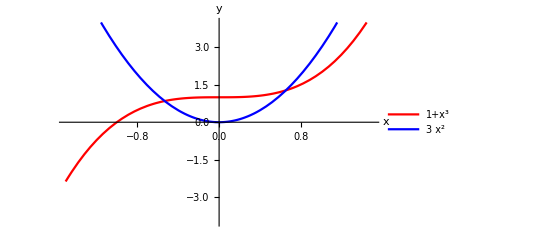

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,-1.5,1.5},PlotRange->{-4,4},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold}, PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

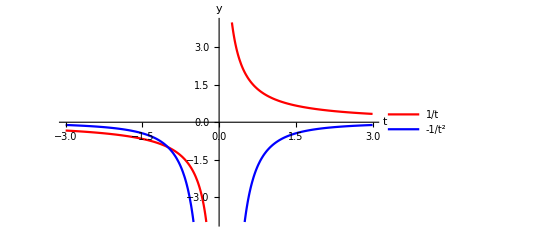

```mathematica
Plot[{Evaluate@g[t],Evaluate@D[g[t],t]},{t, -3,3},PlotRange->{-4,4},AxesLabel->{HoldForm[t],HoldForm[y]},LabelStyle->{"Times New Roman",16,GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

### Differentiability Implies Continuity

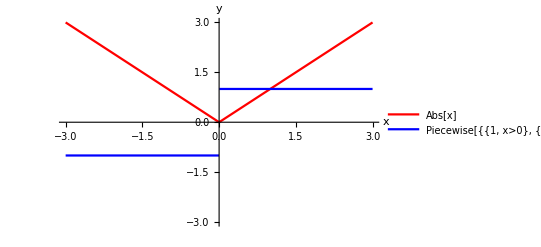

```mathematica
Plot[{Abs[x],Piecewise[{{1,x > 0},{-1, x< 0}}]},{x,-3,3},PlotRange->{-3,3},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12, GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

## Rules of Differential: Functions and Their Derivatives

### Constant Rule

```mathematica
f[x_] := 5
D[f[x],x]
```

0

#### The Plot of Constant Rule

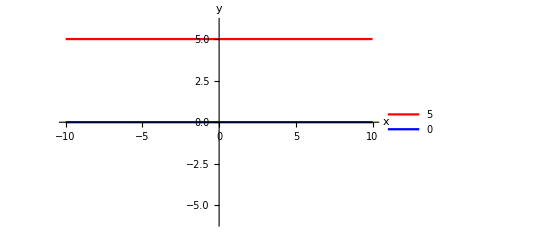

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x, -10,10},PlotRange->{-6,6},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12,GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

### Product Rule

```mathematica
f[x_]:=x^5
D[f[x],x]
```

5 x^4

### The Graph of the Product Rule

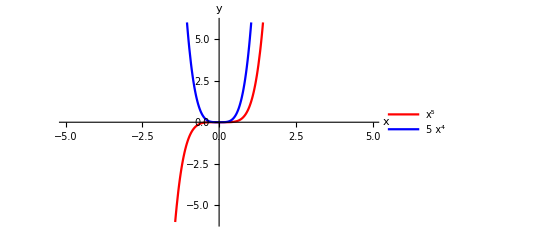

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x, -5,5},PlotRange->{-6,6},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12,GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

### The Sum Rule

```mathematica
Clear[x]
```

```mathematica
f[x_]:= 2 x^2+ 3x
g[x_]:= 5x^2 + 2x
D[{f[x]+g[x]},x]
```

{5+14 x}

```mathematica
{5+14 x}
```

{5+14 x}

### The Plots of Sum Rule

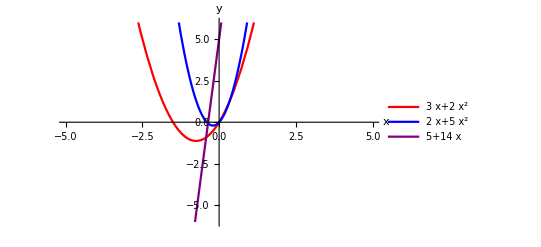

```mathematica
Plot[{Evaluate@f[x],Evaluate@g[x],Evaluate@D[f[x]+ g[x],x]},{x, -5,5},PlotRange->{-6,6},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12,GrayLevel[0],Bold},PlotStyle->{Red,Blue,Purple},PlotLegends->"Expressions"]
```

```mathematica
Clear[x]
```

```mathematica
f[x_]:= 3/x^(1/3) - 2  √x + x^-7
```

```mathematica
D[f[x],x]
```

-7/x^8-1/x^(4/3)-1/(√x)

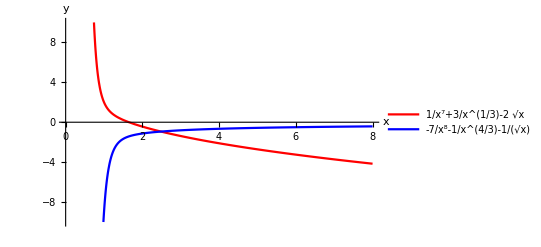

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,0,8},PlotRange->{-10,10},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12,GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

### The Exponet Rule

Exponet Rule The

```mathematica
f[x_]:= Exp[2x]
D[f[x],x]
```

2 ⅇ^(2 x)

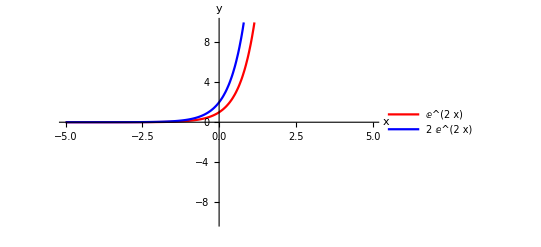

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,-5,5},PlotRange->{-10,10}, AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12,GrayLevel[0],Bold}, PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

### Extrema: Maximum and Minimum

```mathematica
Clear[x,f]
```

```mathematica
f[x_]:= x^3-x
D[f[x],x]
```

-1+3 x^2

```mathematica
Solve[3a^2-1==0,a]
```

{{a→-1/(√3)},{a→1/(√3)}}

```mathematica
max =f[-1/Sqrt[3]];
max
```

2/(3 √3)

```mathematica
min = f[1/Sqrt[3]];
min
```

-2/(3 √3)

#### The Graph of the function and it’s derivative with maxi mun and minimum

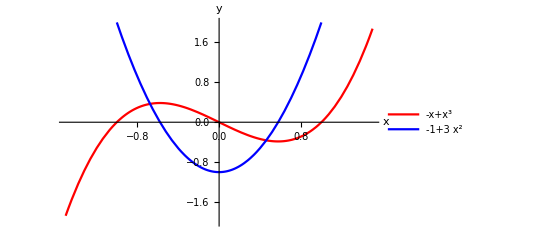

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,-1.5,1.5},PlotRange->{-2,2}, AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12,GrayLevel[0],Bold}, PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

## Concavity and Inflection Point

```mathematica
f[x_] := x^3-x
first =D[f[x],x]
second =f''[x]
```

-1+3 x^2

6 x

### The Plot of the Function and it First and Second Derivative

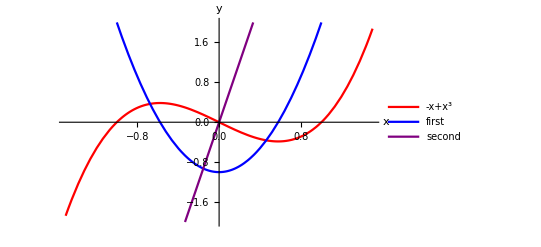

```mathematica
Plot[{Evaluate@f[x],first,second},{x,-1.5,1.5},PlotRange->{-2,2},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->{Red,Blue,Purple},PlotLegends->"Expressions"]
```

```mathematica
f[x_]:= x^4/4+ x^3/3-x^2
firstdev = D[f[x],x];
seconddev = f''[x];
firstdev
seconddev
```

-2 x+x^2+x^3

-2+2 x+3 x^2

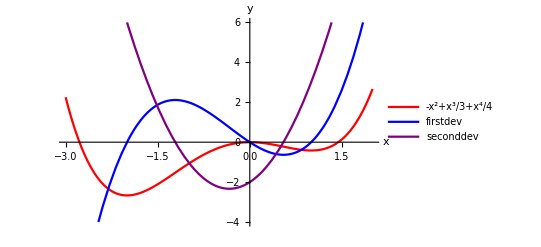

```mathematica
Plot[{Evaluate@f[x],firstdev,seconddev},{x,-3,2},PlotRange->{-4,6},AxesLabel->{HoldForm[x],HoldForm[y]},AxesStyle->{"Times New Roman",12,GrayLevel[0],Bold},PlotStyle->{Red,Blue,Purple},PlotLegends->"Expressions"]
```

## Product Rule

```mathematica
h[x_]:= (x^2+1)* (x-3)
dev =TraditionalForm[D[h[x],x]]
Simplify[dev]
```

x^2+2 (x-3) x+1

3 x^2-6 x+1

## The Plot of a Production Function and Its Derivative

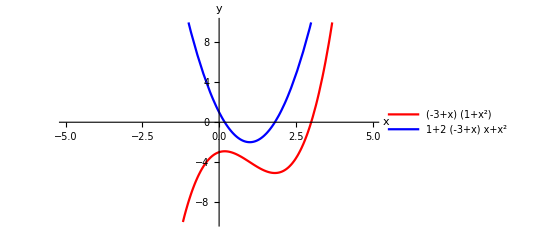

```mathematica
Plot[{Evaluate@h[x],Evaluate@D[h[x],x]},{x,-5,5},PlotRange->{-10,10},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

## The Quotient Rule

```mathematica
f[x_]:= (3x + 5)/(2x - 7)
```

```mathematica
TraditionalForm[D[f[x],x]]
```

3/(2 x-7)-(2 (3 x+5))/(2 x-7)^2

```mathematica
Simplify[3/(-7+2 x)-(2 (5+3 x))/(-7+2 x)^2]
```

-31/(7-2 x)^2

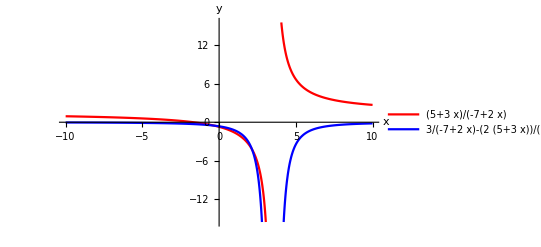

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,-10,10},PlotRange->{-31/2,31/2},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

## The Chain Rule and Its Graph

```mathematica
h[x_]:= (x^2+5)^3
D[h[x],x]
```

6 x (5+x^2)^2

## The Graph of a Composite Function and it’s Derivative

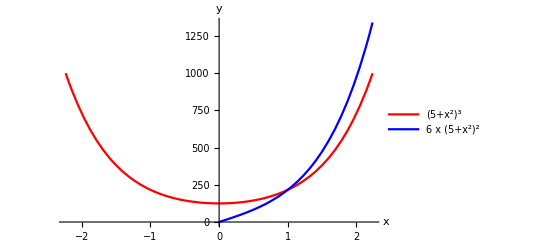

```mathematica
Plot[{Evaluate@h[x],Evaluate@D[h[x],x]},{x,-Sqrt[5],Sqrt[5]},PlotRange->{0, 600*Sqrt[5]}, AxesLabel->{HoldForm[x],HoldForm[y]},AxesStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

## Implicit Differentiation

By default Mathematica treats variables as independent. So for example D{y, x] produces 0. Entering y[x] in place of of y however tells Mathematica to treat y as function of  x. This enables implicit differentiation as in the example below.

We will use implicit differentiation example using the devil’s curve.

Note the format of the code.

#### The Devils’s Curve

```mathematica
eqn = (y[x]^4- 4 y[x]^2== x^4- 9 x^2);
D[eqn,x]
```

-8 y[x] y'[x]+4 y[x]^3 y'[x]==-18 x+4 x^3

```mathematica
Solve[%,y'[x]]
```

{{y'[x]→(-9 x+2 x^3)/(2 y[x] (-2+y[x]^2))}}

The output of Solve [] is a slightly inconvenient form, namely a list of lists of replacement rules. We’ll extract the formula of interest by applying the first (and only) list of y’[x].

```mathematica
m = y'[x]/.%[[1]]
```

(-9 x+2 x^3)/(2 y[x] (-2+y[x]^2))

Let’s now apply this result to plot the devil’s curve together with its tangent lines at the points where x = 1/2.

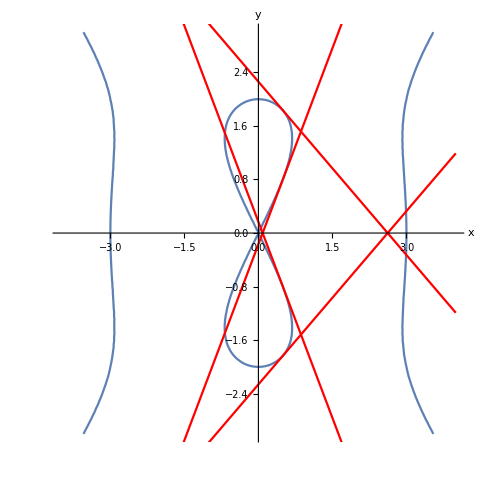

```mathematica
yvals = y/.Solve[y^4-4 y^2==x^4-9 x^2/.x-> 0.5];
tangents = Table[(m/.{x-> 0.5, y[x]-> yvals[[i]]})(x-0.5)+yvals[[i]],{i,4}];

p1 = ContourPlot[y^4-4 y^2== x^4- 9 x^2,{x,-4,4},{y,-3,3}, Axes->True,AxesLabel->{"x","y"},Frame->False,DisplayFunction->Identity];
p2 = Plot[tangents,{x,-4,4},PlotStyle->Red,DisplayFunction->Identity];
Show[p1,p2]
```

## The Derivative of Trigonometric Functions

```mathematica
f[x_]:=Sin[x]
D[f[x],x]
```

Cos[x]

### The Graph of SIn(x) and It’s Derivative

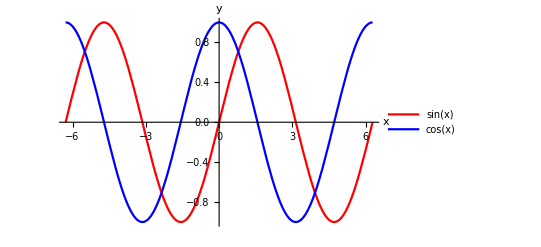

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,-2 Pi,2Pi},PlotRange->{-1,1},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```

```mathematica
f[x_]:= Cos[x]
D[f[x],x]
```

-Sin[x]

## The Graph of Cos(x) and is Derivative

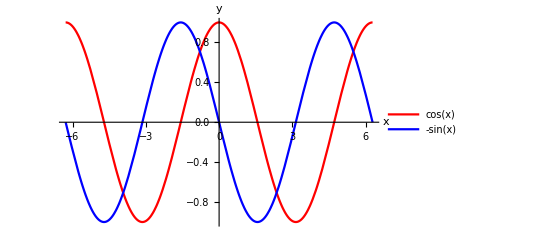

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,-2 Pi,2Pi},PlotRange->{-1,1},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->{Red,Blue},PlotLegends->"Expressions"]
```